```mathematica
SetDirectory[NotebookDirectory[]];
<< Italy2018ElectionDataAnalysis.wl;
```

```mathematica
LoadDataByYear["2014"];
```

No data is available for the year 2014 for the Chamber of Deputies.

No data is available for the year 2014 for the Senate of the Republic.

```mathematica
LoadDataByYear["2018"];
```

Loading the 2018 Chamber of Deputies dataset from cache...

...loaded!

Loading the 2018 Senate of the Republic dataset from cache...

...loaded!

```mathematica
ChamberOfDeputies
```

Chamber of Deputies

```mathematica
SenateOfTheRepublic
```

Senate of the Republic

```mathematica
PlottingElectionElectorsPie[ChamberOfDeputies]
```

-Graphics-

```mathematica
PlottingElectionElectorsPie[SenateOfTheRepublic]
```

-Graphics-

```mathematica
PlottingElectionVotersPie[ChamberOfDeputies, query->"ELETTORI = 13746"]
```

-Graphics-

```mathematica
PlottingElectionVotersNonVotersPie[ChamberOfDeputies]
```

-Graphics-

```mathematica
PlottingElectionVotersNonVotersPie[SenateOfTheRepublic]
```

-Graphics-

```mathematica
PlottingElectionRegionCoalitionsBars[ChamberOfDeputies]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlottingElectionRegionCoalitionsBars[SenateOfTheRepublic]
```

{-Graphics-,-Graphics-,-Graphics-}

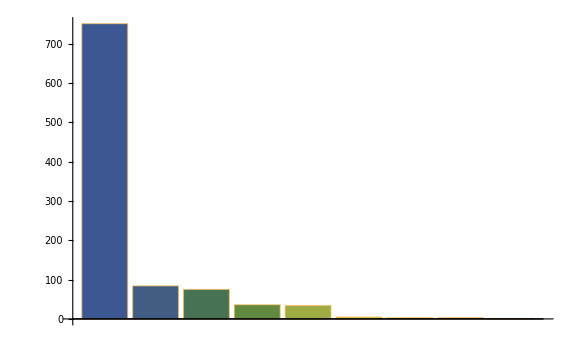

```mathematica
luigidimaio=PlottingCandidate["luigi", "di maio",city->"pomigliano d'arco"]
```

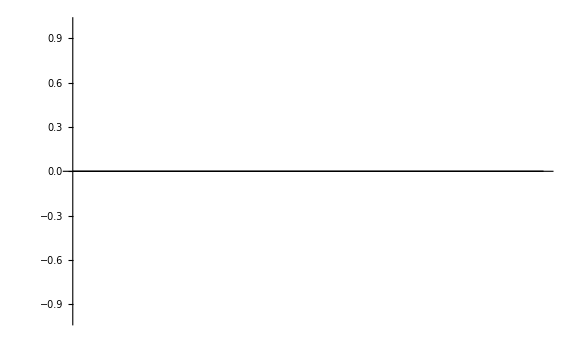

```mathematica
notfound = PlottingCandidate["tommaso","azzalin"]
```